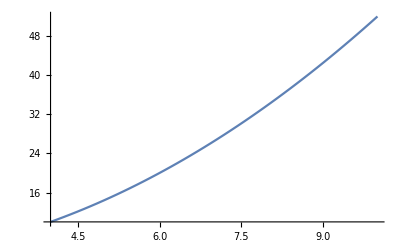

-Graphics3D-

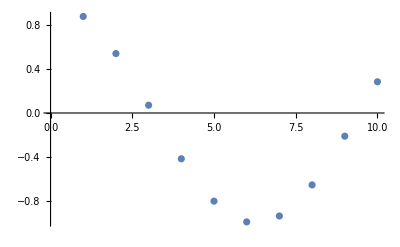

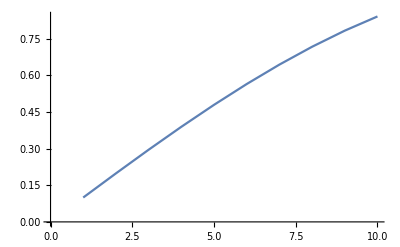

{{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-}}

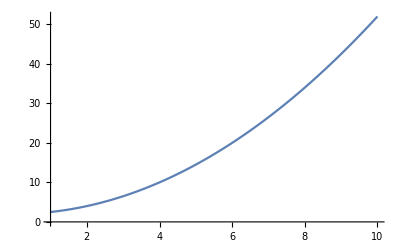
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Clear[f1,f2]
f1[x_]:=x^2/2+2;
f2[x_,y_]:=Cos[x^2+y^2+3];

example1=Plot[f1[x],{x,4,10}]
example2=Plot3D[f2[x,y],{x,-3,3},{y,-2,2}]
example3=ListPlot[Table[{n,Cos[n/2]},{n,10}]]
example4=ListLinePlot[Table[{n,Sin[n/10]},{n,10}]]

table1=Table[{Plot3D[f2[x,y],{x,-1,1},{y,-3,3}],Plot3D[f2[x,y],{x,-3,3},{y,-2,2}]},{x,0,1}]
table2=ParallelTable[{Plot[f1[x],{x,4,10}],Plot[f1[x],{x,1,10}]},{x,0,1}]

FlipView[{table1,table2}]
SlideView[{table1,table2}]
```